# Coupling and distance vs qp and mp

```mathematica
ClearAll["Global`*"]
```

## Parameters

### Physics and known system parameters

```mathematica
hbar=1.05*10^(-34);
eps0=8.85*10^(-12);

(*Paul trap parameters*)
Vcomp=0.68;(*computed using Solve[] in n_vs_gamma notebook to generate 100 Hz difference*)
(*in x-driection*)
dx=0.9*10^(-3);αx=0.93;
V0x=-0.5*V0z*(αz/αx)*(dx/dz)^2+Vcomp;
Vslowx=80;Vfastx=1350;
(*in y-driection*)
dy=0.9*10^(-3);αy=0.93;
V0y=-0.5*V0z*(αz/αy)*(dy/dz)^2-Vcomp;
Vslowy=-80;Vfasty=-1350;
(*in z-driection*)
dz=1.7*10^(-3);αz=0.38;
V0z=56.5;
Vslowz=0;Vfastz=0;

ωslow=2Pi*7*10^(3);ωfast=2Pi*17.5*10^(6);
l=ωslow/ωfast;

(*Ion parameters*)
Qi = 1.6*10^(-19);Mi=40*1.6*10^(-27);
(*We are leaving the nanoparticle parameters free so that they can be varied in the plots*)

(*Mathieu parameters*)
(*for the ion*)
axi=(4*Qi*V0x*αx)/(Mi*ωfast^2*dx^2);qslowxi=(2*Qi*Vslowx*αx)/(Mi*ωslow^2*dx^2);qfastxi=(2*Qi*Vfastx*αx)/(Mi*ωfast^2*dx^2);
ayi=(4*Qi*V0y*αy)/(Mi*ωfast^2*dy^2);qslowyi=(2*Qi*Vslowy*αy)/(Mi*ωslow^2*dy^2);qfastyi=(2*Qi*Vfasty*αy)/(Mi*ωfast^2*dy^2);
azi=(4*Qi*V0z*αz)/(Mi*ωfast^2*dz^2);qslowzi=(4*Qi*Vslowz*αz)/(Mi*ωslow^2*dz^2);qfastzi=(4*Qi*Vfastz*αz)/(Mi*ωfast^2*dz^2);
(*for the nanoparticle*)
(*This defines the Mathieu parameters for the nanoparticle as a function of nanoparticle charge and mass*)
axp[qp_,mp_]:=(4*qp*V0x*αx)/(mp*ωfast^2*dx^2);qslowxp[qp_,mp_]:=(2*qp*Vslowx*αx)/(mp*ωslow^2*dx^2);qfastxp[qp_,mp_]:=(2*qp*Vfastx*αx)/(mp*ωfast^2*dx^2);
ayp[qp_,mp_]:=(4*qp*V0y*αy)/(mp*ωfast^2*dy^2);qslowyp[qp_,mp_]:=(2*qp*Vslowy*αy)/(mp*ωslow^2*dy^2);qfastyp[qp_,mp_]:=(2*qp*Vfasty*αy)/(mp*ωfast^2*dy^2);
azp[qp_,mp_]:=(4*qp*V0z*αz)/(mp*ωfast^2*dz^2);qslowzp[qp_,mp_]:=(4*qp*Vslowz*αz)/(mp*ωslow^2*dz^2);qfastzp[qp_,mp_]:=(4*qp*Vfastz*αz)/(mp*ωfast^2*dz^2);
```

### Effective secular trap frequencies

```mathematica
(*for the ion*)
Ωxi=1/(√2)((ωfast/2 √(axi+qfastxi^2/2))^2+ωslow^2/4+√(((ωfast/2 √(axi+qfastxi^2/2))^2-ωslow^2/4)^2-(qslowxi^2*ωslow^4)/8))^(1/2);
Ωyi=1/(√2)((ωfast/2 √(ayi+qfastyi^2/2))^2+ωslow^2/4+√(((ωfast/2 √(ayi+qfastyi^2/2))^2-ωslow^2/4)^2-(qslowyi^2*ωslow^4)/8))^(1/2);
Ωzi=1/(√2)((ωfast/2 √(azi+qfastzi^2/2))^2+ωslow^2/4+√(((ωfast/2 √(azi+qfastzi^2/2))^2-ωslow^2/4)^2-(qslowzi^2*ωslow^4)/8))^(1/2);
(*for the nanoparticle*)
Ωxp[qp_,mp_]:=ωfast/2 √(axp[qp,mp]+(qslowxp[qp,mp]^2*l^2)/2+qfastxp[qp,mp]^2/2);
Ωyp[qp_,mp_]:=ωfast/2 √(ayp[qp,mp]+(qslowyp[qp,mp]^2*l^2)/2+qfastyp[qp,mp]^2/2);
Ωzp[qp_,mp_]:=ωfast/2 √(azp[qp,mp]+(qslowzp[qp,mp]^2*l^2)/2+qfastzp[qp,mp]^2/2);
```

### Distance between ion and nanoparticle

```mathematica
d[qp_,mp_]:=((Qi*qp)/(4*Pi*eps0)*(1/(Mi*Ωzi^2)+1/(mp*Ωzp[qp,mp]^2)))^(1/3);
```

### Trap frequency renormalisations and couplings

```mathematica
(*for the ion*)
(*in x-driection*)
newΩxi[qp_,mp_]:=Sqrt[Ωxi^2-(Qi*qp)/(4*Pi*eps0*Mi*d[qp,mp]^3)];(*this is the formula for x-axis, z-axis is different*)
xzpfi[qp_,mp_]:=√(hbar/(2*Mi*newΩxi[qp,mp]));
(*in y-driection*)
newΩyi[qp_,mp_]:=Sqrt[Ωyi^2-(Qi*qp)/(4*Pi*eps0*Mi*d[qp,mp]^3)];(*this is the formula for y-axis, z-axis is different*)
yzpfi [qp_,mp_]:=√(hbar/(2*Mi*newΩyi[qp,mp]));
(*in z-driection*)
newΩzi[qp_,mp_]:=Sqrt[Ωzi^2+2*(Qi*qp)/(4*Pi*eps0*Mi*d[qp,mp]^3)];(*this is the formula for the z-axis*)
zzpfi [qp_,mp_]:= √(hbar/(2*Mi*newΩzi[qp,mp]));
(*for the nanoparticle*)
(*in x-driection*)
newΩxp[qp_,mp_]:=Sqrt[Ωxp[qp,mp]^2-(Qi*qp)/(4*Pi*eps0*mp*d[qp,mp]^3)];(*this is the formula for x-axis, z-axis is different*)
xzpfp[qp_,mp_]:=√(hbar/(2*mp*newΩxp[qp,mp]));
(*in y-driection*)
newΩyp[qp_,mp_]:=Sqrt[Ωyp[qp,mp]^2-(Qi*qp)/(4*Pi*eps0*mp*d[qp,mp]^3)];(*this is the formula for y-axis, z-axis is different*)
yzpfp[qp_,mp_]:=√(hbar/(2*mp*newΩyp[qp,mp]));
(*in z-driection*)
newΩzp[qp_,mp_]:=Sqrt[Ωzp[qp,mp]^2+2*(Qi*qp)/(4*Pi*eps0*mp*d[qp,mp]^3)];(*this is the formula for the z-axis*)
zzpfp[qp_,mp_]:=√(hbar/(2*mp*newΩzp[qp,mp]));
```

### Couplings

```mathematica
gx[qp_,mp_]:=1/hbar(Qi*qp)/(4*Pi*eps0)(xzpfi[qp,mp]*xzpfp[qp,mp])/d[qp,mp]^3;(*in x-driection*)
gy[qp_,mp_]:=1/hbar(Qi*qp)/(4*Pi*eps0)(yzpfi[qp,mp]*yzpfp[qp,mp])/d[qp,mp]^3;(*in y-driection*)
gz[qp_,mp_]:=-1/hbar(Qi*qp)/(2*Pi*eps0)(zzpfi[qp,mp]*zzpfp[qp,mp])/d[qp,mp]^3;(*in z-driection*)
```

## Plots

### Coupling, distance vs nanoparticle mass

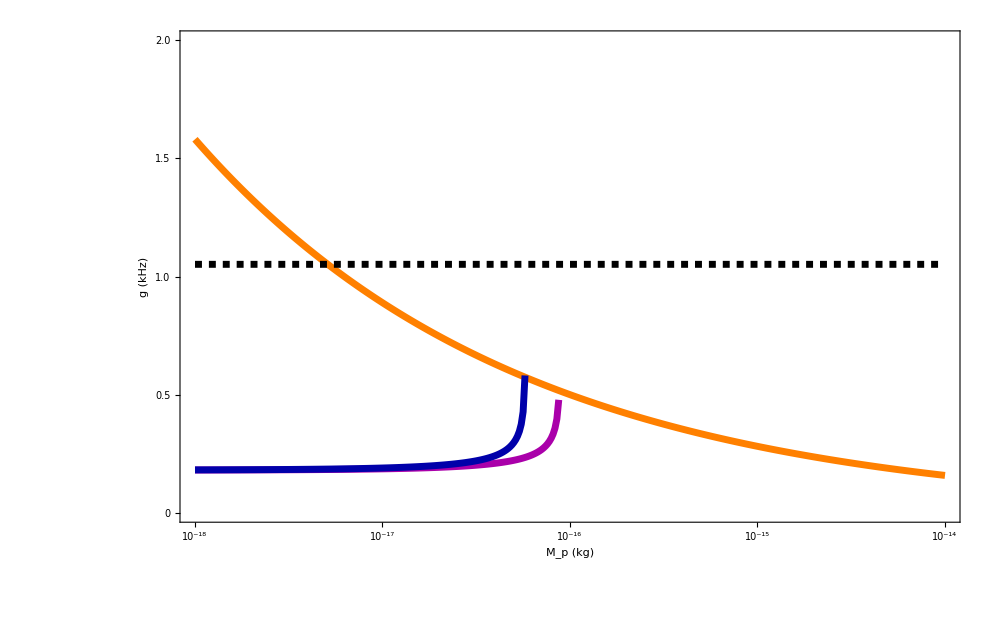

```mathematica
(*1. Desired Axes Ranges*)
xRange={10^(-18),10^(-14)};
yRangeLeft={0,2};
yRangeRight={0,100};

(*2. Raw Data for Plots*)
(*Generate {x,y} data points for the left-axis plots*)
dataLeft1=Table[{mp,(gx[qp,mp]/(2*Pi*10^3))/. {qp->750*Qi}},{mp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];
dataLeft2=Table[{mp,(gy[qp,mp]/(2*Pi*10^3))/. {qp->750*Qi}},{mp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];
dataLeft3=Table[{mp,(-gz[qp,mp]/(2*Pi*10^3))/. {qp->750*Qi}},{mp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];
(*Generate {x,y} data points for the right-axis plot*)
dataRight=Table[{mp,(d[qp,mp]/10^-6)/. {qp->750*Qi}},{mp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];

(*3. Rescale the Right-Axis Data*)
(*This maps the y-values from dataRight from their original range (yRangeRight) into the target range of the left axis (yRangeLeft) so that we can have a two-sided plot in which the left-side and right-side data have vastly different ranges*)
rescaledDataRight={#[[1]],Rescale[#[[2]],yRangeRight,yRangeLeft]}&/@dataRight;

(*4. Custom Ticks for All Axes*)
(*Ticks for the LEFT axis*)
yticksLeftCustom={{0,"0"},{0.5,"0.5"},{1.0,"1.0"},{1.5,"1.5"},{2.0,"2.0"},{2.5,"2.5"}};
(*Ticks for the RIGHT axis: positions are rescaled, labels are original values*)
(*This defines scaled tick marks so that the right-side axis has tick marks according to unscaled values of the right-side data*)
yticksRightCustom=Table[{Rescale[y,yRangeRight,yRangeLeft],y},{y,20,100,20}];

(*5. Plot Everything*)
ListLogLinearPlot[
{dataLeft3,dataLeft1,dataLeft2,rescaledDataRight },
Joined->True,
PlotStyle->{
{Thickness[0.005],Orange},
{Thickness[0.005],Darker[Magenta]},
{Thickness[0.005],Darker[Blue]},
{Dashed,Thickness[0.005],Black}
},
Frame->True,
FrameStyle->Directive[Black,Thick,25],
GridLines->Automatic,
GridLinesStyle->Directive[Thickness[0.003],Opacity[0.3],Gray],
ImageSize->1000,
PlotRange->{xRange,yRangeLeft},
FrameTicks->{{yticksLeftCustom,yticksRightCustom},{Automatic,None}},
FrameLabel->{{Style["g (kHz)",18],Style["D (μm)",18]},{Style["M_p (kg)",18],None}}]
```

### Coupling, distance vs nanoparticle charge

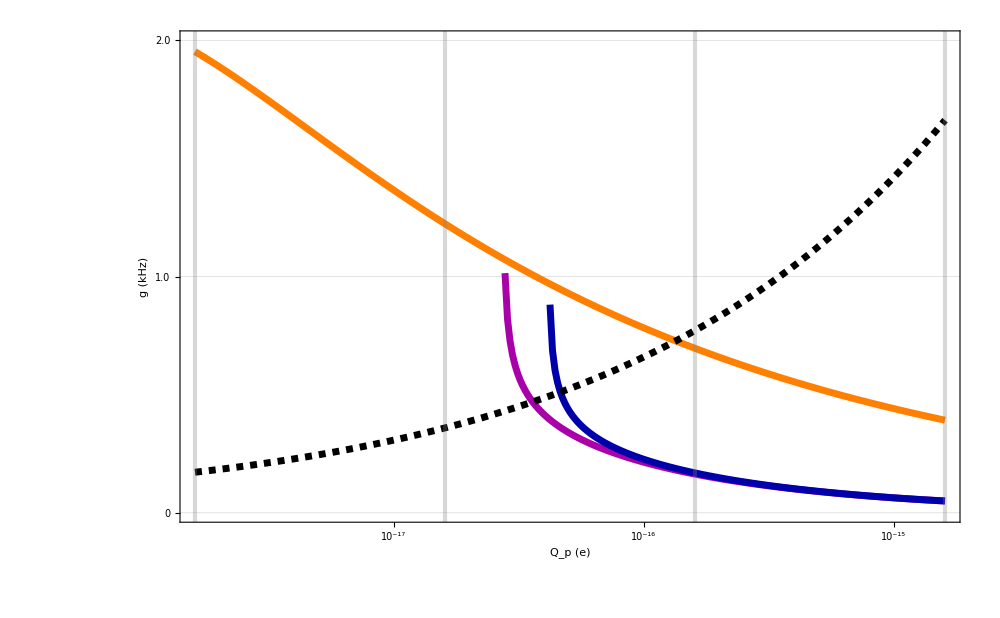

```mathematica
(*1. Desired Axes Ranges*)
xRange={10*Qi,10000*Qi};
yRangeLeft={0,2};
yRangeRight={0,150};

(*2. Raw Data for Plots*)
(*Generate {x,y} data points for the left-axis plots*)
dataLeft1=Table[{qp,(gx[qp,mp]/(2*Pi*10^3))/. {mp->2*10^(-17)}},{qp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];
dataLeft2=Table[{qp,(gy[qp,mp]/(2*Pi*10^3))/. {mp->2*10^(-17)}},{qp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];
dataLeft3=Table[{qp,(-gz[qp,mp]/(2*Pi*10^3))/. {mp->2*10^(-17)}},{qp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];
(*Generate {x,y} data points for the right-axis plot*)
dataRight=Table[{qp,(d[qp,mp]/10^-6)/. {mp->2*10^(-17)}},{qp,10^Range[Log10[xRange[[1]]],Log10[xRange[[2]]],0.01]}];

(*3. Rescale the Right-Axis Data*)
(*This maps the y-values from dataRight from their original range (yRangeRight) into the target range of the left axis (yRangeLeft) so that we can have a two-sided plot in which the left-side and right-side data have vastly different ranges*)
rescaledDataRight={#[[1]],Rescale[#[[2]],yRangeRight,yRangeLeft]}&/@dataRight;

(*4. Custom Ticks for All Axes*)
xticksCustom={{10*Qi,"10"},{100*Qi,"100"},{1000*Qi,"1000"},{10000*Qi,"10000"}};
(*Ticks for the LEFT axis*)
yticksLeftCustom={{0,"0"},{1.0,"1.0"},{2.0,"2.0"},{3.0,"3.0"},{4.0,"4.0"},{5.0,"5.0"},{6.0,"6.0"}};
(*Ticks for the RIGHT axis: positions are rescaled, labels are original values*)
(*This defines scaled tick marks so that the right-side axis has tick marks according to unscaled values of the right-side data*)
yticksRightCustom=Table[{Rescale[y,yRangeRight,yRangeLeft],y},{y,0,250,50}];

(* ::Section::*)
(*5. Plot Everything*)
ListLogLinearPlot[
{dataLeft1,dataLeft2,dataLeft3,rescaledDataRight },
Joined->True,
PlotStyle->{{Thickness[0.005],Darker[Magenta]},{Thickness[0.005],Darker[Blue]},{Thickness[0.005],Orange},{Dashed,Thickness[0.005],Black}},
Frame->True,
FrameStyle->Directive[Black,Thick,25],
GridLines->{{10*Qi,100*Qi,1000*Qi,10000*Qi},Automatic},
GridLinesStyle->Directive[Thickness[0.003],Opacity[0.3],Gray],
ImageSize->1000,
PlotRange->{xRange,yRangeLeft},
FrameTicks->{{yticksLeftCustom,yticksRightCustom},{xticksCustom,None}},
FrameLabel->{{Style["g (kHz)",18],Style["D (μm)",18]},{Style["Q_p (e)",18],None}}]
```